## Дополнительные функции:

```mathematica
MakeTable[{points_,fValues_,norms_}]:=Module[{gridLabel,gridData},
gridLabel={"k","(X^k)","f(X^k)","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],4]]<>", "<>ToString[SetAccuracy[points[[i,2]],4]]<>" )"];
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,4];
(*в 4-м столбце-значение нормы невязки*)
gridData[[All,4]]=SetAccuracy[norms,4];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
];
PlotMethod[func_,setX_,setY_,{points_,fValues_}]:=Module[{},
ContourPlot[func[{x,y}],setX,setY,Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,Epilog->{Purple,Thickness[0.001],Arrowheads[.02],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}]
];
PlotNorms[norms_]:=Module[{},
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
];
Antigrad[point_, unc_] := -Grad[func[{x, y}], {x, y}] /. {x->point[[1]],y->point[[2]]};
```

## Алгоритм

```mathematica
Algorithm[{x0_, y0_},func_,ϵ_, method_] := Module [
{
X = {{x0, y0}},
y = {},
w= {},
norms = {},
A = IdentityMatrix[2],
dA = {},
dX = {},
dw = {},
p = 0,
κ = 0
},

y ={ func[Last@X] };
p = Antigrad[Last@X, func];
w = {p};
norms = {Norm[Last@w]};
While[Last@norms ≥ ϵ,
κ = NArgMin[func[Last@X + α * p], α];
dX = κ * p;
AppendTo[X, Last@X + dX ];
AppendTo[y, func[Last@X]];
AppendTo[w, Antigrad[Last@X, func]];
AppendTo[norms, Norm@Last@w];
dw = w[[-1]] - w[[-2]];
dA =method[A, dX, dw];
A += dA;
p = A.Last@w;
] ;
{X, y, norms}
];
```

## Методы вычисления ΔA

```mathematica
DavidFletcherPauell[A_,dX_, dw_] :=-KroneckerProduct[dX, dX]/(dw.dX)-KroneckerProduct[A.dw, A.dw]/((A.dw).dw);
BroidenPauellGoldfarbShenno[A_,dX_, dw_] := DavidFletcherPauell[A, dX, dw] -(A.dw).dw * KroneckerProduct[(A.dw)/((A.dw).dw)-dX/(dw.dX), (A.dw)/((A.dw).dw)-dX/(dw.dX)];
Pauell[A_,dX_, dw_]  := -KroneckerProduct[dX + A.dw, dX + A.dw]/(dw.(dX + A.dw));
McKormick[A_,dX_, dw_]:= -KroneckerProduct[dX,dX]/(dw.dX)- (A dw Transpose@dX)/(Transpose[dX].dw);
```

```mathematica
a = IdentityMatrix[2]; dx = {1, 1}; dw = Antigrad[dx, f];
```

```mathematica
McKormick[a, dx, dw]
```

Transpose::nmtx: The first two levels of {1,1} cannot be transposed.

{{-1/(-func^({0,1})[{1,1}]-func^({1,0})[{1,1}])+(Transpose[{1,1}] func^({1,0})[{1,1}])/(Transpose[{1,1}].{-func^({1,0})[{1,1}],-func^({0,1})[{1,1}]}),-1/(-func^({0,1})[{1,1}]-func^({1,0})[{1,1}])},{-1/(-func^({0,1})[{1,1}]-func^({1,0})[{1,1}]),(Transpose[{1,1}] func^({0,1})[{1,1}])/(Transpose[{1,1}].{-func^({1,0})[{1,1}],-func^({0,1})[{1,1}]})-1/(-func^({0,1})[{1,1}]-func^({1,0})[{1,1}])}}

## Функции:

```mathematica
f[{x_,y_}]:=6 x^2+3 y^2-4x y+4 √5(x+2y)+22;
g[{x_,y_}]:=8 x^2+5 y^2-4x y + 8 √5(x+2y)+64;
rosenbrok[{x_,y_}]:=(1-x)^2+200(y-x^2)^2;
```

## Вычисления:

### Первый пример:

```mathematica
func =g;(*x0 = {√5,0}, x1 = {0 , 2 √5}*)
method = Pauell;
Res = Algorithm[{0,2 √5}, func, 0.001, method];
X = Res[[1]];
Y = Res[[2]];
norms = Res[[3]];
setX = {x,-7,7};
setY ={y,-7,7};
```

### Второй пример:

```mathematica
func =rosenbrok;(*x0 = {-1,-2}*)
method = Pauell;
Res = Algorithm[{-1,-2}, func, 0.001, method];
X = Res[[1]];
Y = Res[[2]];
norms = Res[[3]];
setX = {x,-7,7};
setY ={y,-7,7};
```

### Результаты:

-Graphics-

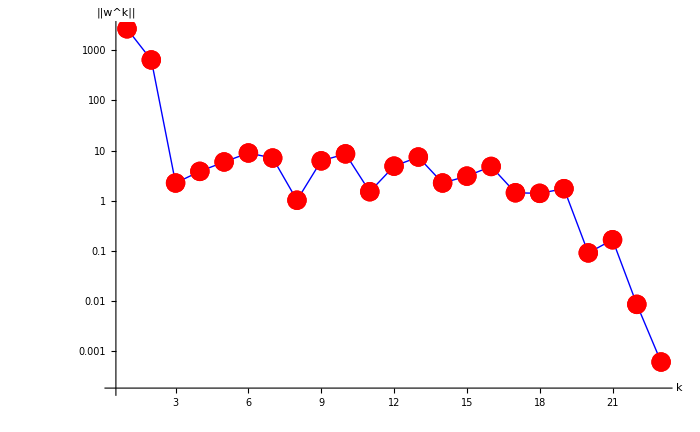

k | (X^k) | f(X^k) | ||w^k||
0 | ( -1.000, -2.000 ) | 1804. | 2687.
1 | ( 0.251, -1.376 ) | 414.441 | 643.121
2 | ( -0.069, 0.004 ) | 1.143 | 2.268
3 | ( -0.053, 0.011 ) | 1.124 | 3.866
4 | ( 0.094, -0.006 ) | 0.865 | 5.958
5 | ( 0.150, 0. ) | 0.822 | 8.992
6 | ( 0.380, 0.129 ) | 0.433 | 7.125
7 | ( 0.371, 0.136 ) | 0.396 | 1.028
8 | ( 0.486, 0.223 ) | 0.296 | 6.268
9 | ( 0.601, 0.346 ) | 0.203 | 8.632
10 | ( 0.612, 0.375 ) | 0.151 | 1.52
11 | ( 0.696, 0.477 ) | 0.105 | 4.911
12 | ( 0.762, 0.570 ) | 0.08 | 7.47
13 | ( 0.793, 0.631 ) | 0.044 | 2.268
14 | ( 0.850, 0.719 ) | 0.026 | 3.106
15 | ( 0.893, 0.792 ) | 0.019 | 4.845
16 | ( 0.921, 0.849 ) | 0.007 | 1.449
17 | ( 0.955, 0.910 ) | 0.003 | 1.411
18 | ( 0.984, 0.967 ) | 0.001 | 1.747
19 | ( 0.987, 0.974 ) | 0.0002 | 0.092
20 | ( 0.999, 0.997 ) | 0. | 0.168
21 | ( 1.00, 0.999 ) | 0. | 0.009
22 | ( 1.00, 1.00 ) | 0. | 0.0006

```mathematica
PlotMethod[func,setX,setY,{X, Y}]
PlotNorms[norms]
MakeTable[Res]
```